2.1852×10^-23

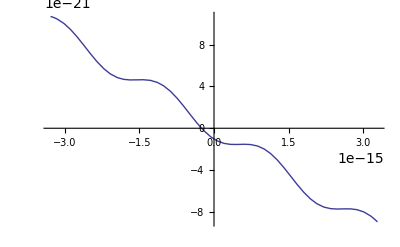

```mathematica
Delta=200*10^-6;
Rn=100;
Ic=Pi*Delta/(2*Rn);
Ib =.95*Ic;
planck=4.1357*10^-15;
e=1.602*10^-19;
Phi0=planck/(2*2*Pi);
U[p_]:=-Phi0*Ic*Cos[p/Phi0]-Ib*p
U[(Pi-ArcSin[.95])*Phi0]-U[ArcSin[.95]*Phi0]
Plot[U[phi],{phi,-10*Phi0,10*Phi0}]
```

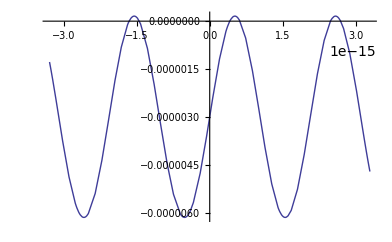

```mathematica
Plot[U'[phi],{phi,-10*Phi0,10*Phi0}]
```